```mathematica
N[2^(1/12)]
```

1.05946

```mathematica
N[2^(-1/12)]
```

0.943874

```mathematica
NestList[(#/(2^(1/12)) &), 1, 12]
```

{1,1/2^(1/12),1/2^(1/6),1/2^(1/4),1/2^(1/3),1/2^(5/12),1/(√2),1/2^(7/12),1/2^(2/3),1/2^(3/4),1/2^(5/6),1/2^(11/12),1/2}

```mathematica
%//N
```

{1.,0.943874,0.890899,0.840896,0.793701,0.749154,0.707107,0.66742,0.629961,0.594604,0.561231,0.529732,0.5}

```mathematica
frets=NestList[(#/(2^(1/12)) &), 1, 12]
```

{1,1/2^(1/12),1/2^(1/6),1/2^(1/4),1/2^(1/3),1/2^(5/12),1/(√2),1/2^(7/12),1/2^(2/3),1/2^(3/4),1/2^(5/6),1/2^(11/12),1/2}

```mathematica
frets
```

{1,1/2^(1/12),1/2^(1/6),1/2^(1/4),1/2^(1/3),1/2^(5/12),1/(√2),1/2^(7/12),1/2^(2/3),1/2^(3/4),1/2^(5/6),1/2^(11/12),1/2}

```mathematica
FretPosition[n_]:=2^(-n/12)
```

```mathematica
FretPosition[2]
```

1/2^(1/6)

```mathematica
FretPosition[0]
```

1

```mathematica
FretPosition[12]
```

1/2

```mathematica
FretPosition[13]
```

1/(2 2^(1/12))

```mathematica
FretPosition /@ {0,1,2,3,4,5,6,7,8,9,10,11,12,13} //N
```

{1.,0.943874,0.890899,0.840896,0.793701,0.749154,0.707107,0.66742,0.629961,0.594604,0.561231,0.529732,0.5,0.471937}

```mathematica
Clear[FretPosition];
FretPosition[n_]:=1-2^(-n/12);
fretlength=0.05;
fretoverlength=0.0025;
numfrets=13;
fretPositions=FretPosition /@ Range[0,numfrets]
frets=(Line[{{#,0-fretoverlength},{#,fretlength+fretoverlength}}] &) /@ fretPositions ;
PrependTo[frets, Thickness[0.005]];
PrependTo[frets, CapForm["Round"]];
```

{0,1-1/2^(1/12),1-1/2^(1/6),1-1/2^(1/4),1-1/2^(1/3),1-1/2^(5/12),1-1/(√2),1-1/2^(7/12),1-1/2^(2/3),1-1/2^(3/4),1-1/2^(5/6),1-1/2^(11/12),1/2,1-1/(2 2^(1/12))}

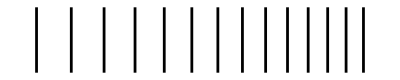

-Graphics-

```mathematica
Graphics[frets]
```

```mathematica
Prepend[frets, Thickness[0.005]]
```

{Thickness[0.005],CapForm[Round],Thickness[0.005],Line[{{1,-0.0025},{1,0.0525}}],Line[{{1/2^(1/12),-0.0025},{1/2^(1/12),0.0525}}],Line[{{1/2^(1/6),-0.0025},{1/2^(1/6),0.0525}}],Line[{{1/2^(1/4),-0.0025},{1/2^(1/4),0.0525}}],Line[{{1/2^(1/3),-0.0025},{1/2^(1/3),0.0525}}],Line[{{1/2^(5/12),-0.0025},{1/2^(5/12),0.0525}}],Line[{{1/(√2),-0.0025},{1/(√2),0.0525}}],Line[{{1/2^(7/12),-0.0025},{1/2^(7/12),0.0525}}],Line[{{1/2^(2/3),-0.0025},{1/2^(2/3),0.0525}}],Line[{{1/2^(3/4),-0.0025},{1/2^(3/4),0.0525}}],Line[{{1/2^(5/6),-0.0025},{1/2^(5/6),0.0525}}],Line[{{1/2^(11/12),-0.0025},{1/2^(11/12),0.0525}}],Line[{{1/2,-0.0025},{1/2,0.0525}}],Line[{{1/(2 2^(1/12)),-0.0025},{1/(2 2^(1/12)),0.0525}}]}

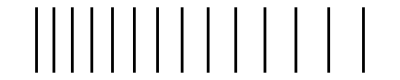

```mathematica
Graphics[%]
```

```mathematica
stringOverlength=0.0025;
stringSpacing=fretlength/5;
strings=(Line[{{FretPosition[0]+stringOverlength,#*stringSpacing},{FretPosition[numfrets]-stringOverlength,#*stringSpacing}}] &)/@{0,1,2,3,4,5};
PrependTo[strings, Gray]
```

{GrayLevel[0.5],Line[{{0.0025,0.},{0.525563,0.}}],Line[{{0.0025,0.01},{0.525563,0.01}}],Line[{{0.0025,0.02},{0.525563,0.02}}],Line[{{0.0025,0.03},{0.525563,0.03}}],Line[{{0.0025,0.04},{0.525563,0.04}}],Line[{{0.0025,0.05},{0.525563,0.05}}]}

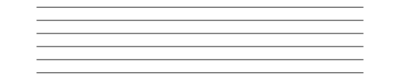

```mathematica
Graphics[strings]
```

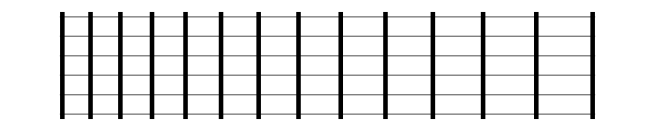

```mathematica
Graphics[{strings,frets}]
```

```mathematica
dotSize=stringSpacing*0.5;
DotPosition[s_, f_]:={FretPosition[f]-dotSize*1.5,(s-1)*stringSpacing}
```

```mathematica
DotPosition[2,3]
```

{0.835396,0.02}

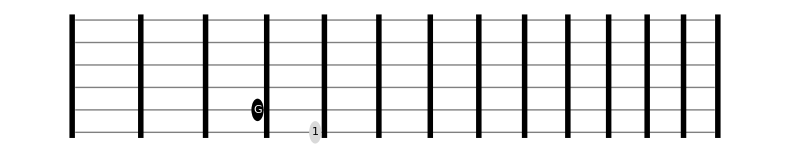

```mathematica
Graphics[{strings, frets, {Black, Disk[DotPosition[2,3], dotSize],White,Text["G",DotPosition[2,3],{0,0}]},{LightGray, Disk[DotPosition[1,4],dotSize],Black,Text["1",DotPosition[1,4],{0,0}]}}]
```

```mathematica
BlackDot[s_,f_,label_]:={Black, Disk[DotPosition[s,f], dotSize],White,Text[label,DotPosition[s,f],{0,0}]};
LightGrayDot[s_,f_,label_]:={LightGray, Disk[DotPosition[s,f], dotSize],Black,Text[label,DotPosition[s,f],{0,0}]};
DarkGrayDot[s_,f_,label_]:={Gray, Disk[DotPosition[s,f], dotSize],White,Text[label,DotPosition[s,f],{0,0}]};
```

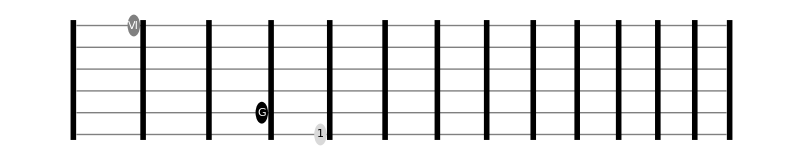

```mathematica
Graphics[{strings,frets, BlackDot[2,3,"G"],LightGrayDot[1,4,"1"],DarkGrayDot[6,1,"VI"]}]
```

```mathematica
ClearAll[FretBoard,FretPosition,DotPosition,StringPosition];
FretPosition[n_]:=1-2^(-n/12);
numStrings=6;
StringPos[n_]:=(numStrings-n)*stringSpacing;
DotPosition[s_, f_]:={FretPosition[f]-dotSize*1.5,StringPos[s]};
DotPosition[s_,0]:={FretPosition[f],StringPos[s]};
Options[FretBoard]={
fretLength->0.05,
fretOverLength->0.0025,
stringOverLength->0,
stringColor->Gray,
stringThickness->Thin,
fretColor->Black,
fretThickness->Thickness[0.005],
dotList->{},
Markers->Nothing
};
FretBoard[numFrets_Integer,OptionsPattern[]]:=
Block[{
stringSpacing=OptionValue[fretLength]/5,
dotSize=OptionValue[fretLength]/10,
fretPositions=FretPosition /@ Range[0,numFrets],
frets=(Line[{{#,0-OptionValue[fretOverLength]},{#,OptionValue[fretLength]+OptionValue[fretOverLength]}}] &) /@ fretPositions ,
strings=(Line[{{FretPosition[0]-OptionValue[stringOverLength],StringPos[#]},{FretPosition[numFrets]+OptionValue[stringOverLength],StringPos[#]}}] &)/@{1,2,3,4,5,6}
},
Graphics[{OptionValue[fretThickness],CapForm["Round"],OptionValue[fretColor],(Line[{{#,0-OptionValue[fretOverLength]},{#,OptionValue[fretLength]+OptionValue[fretOverLength]}}] &) /@ fretPositions, 
OptionValue[stringThickness],OptionValue[stringColor],
strings,
MapIndexed[OptionValue[Markers], FretboardNoteNames[{0,numFrets}],{2}]
}
]
]
```

ClearAll::wrsym: Symbol StringPosition is Protected.

```mathematica
Options[FretBoard]
```

{fretLength→0.05,fretOverLength→0.0025,stringOverLength→0,stringColor→GrayLevel[0.5],stringThickness→Thickness[Tiny],fretColor→GrayLevel[0],fretThickness→Thickness[0.005],dotList→{},Markers→Nothing}

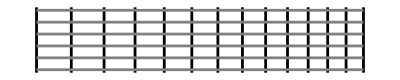

```mathematica
FretBoard[13]
```

```mathematica
FretBoard[7,Markers->CMajorScale]
```

-Graphics-

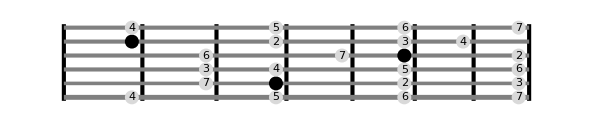

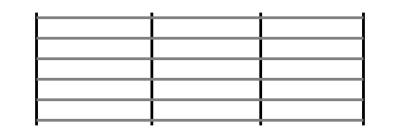

```mathematica
FretBoard[3]
```

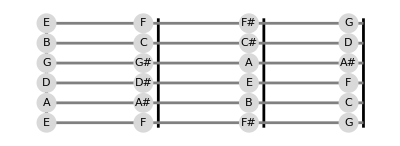

```mathematica
FretBoard[3,Markers->LabelAllNotes]
```

```mathematica
BlackDot[1,3,"G"]
```

{GrayLevel[0],Disk[{1-1/2^(1/4)-1.5 dotSize,0},dotSize],GrayLevel[1],Text[G,{1-1/2^(1/4)-1.5 dotSize,0},{0,0}]}

```mathematica
ClearAll[FretboardNotes];
noteNumbers=<|"E"->1,"F"->2,"F#"->3,"G"->4,"G#"->5,"A"->6,"A#"->7,"B"->8,"C"->9,"C#"->10,"D"->11,"D#"->12|>
noteNames=Association[KeyValueMap[{#2->#} &,noteNumbers]]
StandardTuning={"E","B","G","D","A","E"}
Options[FretboardNotes]={
Tuning->StandardTuning
};
Options[FretboardNoteNames]={
Tuning->StandardTuning
};
FretboardNotes[{bottom_Integer, top_Integer}, OptionsPattern[]]:=
(Mod[Range[bottom,top]+#, 12, 1] &) /@ Lookup[noteNumbers, OptionValue[Tuning]];
FretboardNoteNames[{bottom_Integer, top_Integer}, OptionsPattern[]]:=
Map[(noteNames[[#]] &), FretboardNotes[{bottom,top},Tuning->OptionValue[Tuning]], {2}]
```

```mathematica
Options[FretboardNotesFretNumbers]={
Tuning->StandardTuning
};
FretboardNotesFretNumbers[{bottom_Integer, top_Integer}, OptionsPattern[]]:=
Inner[List,#,Range[0,12],List] & /@ FretboardNoteNames[{bottom,top},Tuning->OptionValue[Tuning]]
```

```mathematica
FretboardNotesFretNumbers[{0,12}]
```

{{{E,0},{F,1},{F#,2},{G,3},{G#,4},{A,5},{A#,6},{B,7},{C,8},{C#,9},{D,10},{D#,11},{E,12}},{{B,0},{C,1},{C#,2},{D,3},{D#,4},{E,5},{F,6},{F#,7},{G,8},{G#,9},{A,10},{A#,11},{B,12}},{{G,0},{G#,1},{A,2},{A#,3},{B,4},{C,5},{C#,6},{D,7},{D#,8},{E,9},{F,10},{F#,11},{G,12}},{{D,0},{D#,1},{E,2},{F,3},{F#,4},{G,5},{G#,6},{A,7},{A#,8},{B,9},{C,10},{C#,11},{D,12}},{{A,0},{A#,1},{B,2},{C,3},{C#,4},{D,5},{D#,6},{E,7},{F,8},{F#,9},{G,10},{G#,11},{A,12}},{{E,0},{F,1},{F#,2},{G,3},{G#,4},{A,5},{A#,6},{B,7},{C,8},{C#,9},{D,10},{D#,11},{E,12}}}

```mathematica
Inner[List,#,Range[0,12],List] &/@FretboardNotes[{0,12}]
```

{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},{9,8},{10,9},{11,10},{12,11},{1,12}},{{8,0},{9,1},{10,2},{11,3},{12,4},{1,5},{2,6},{3,7},{4,8},{5,9},{6,10},{7,11},{8,12}},{{4,0},{5,1},{6,2},{7,3},{8,4},{9,5},{10,6},{11,7},{12,8},{1,9},{2,10},{3,11},{4,12}},{{11,0},{12,1},{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12}},{{6,0},{7,1},{8,2},{9,3},{10,4},{11,5},{12,6},{1,7},{2,8},{3,9},{4,10},{5,11},{6,12}},{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},{9,8},{10,9},{11,10},{12,11},{1,12}}}

```mathematica
FretboardNotes[{1,12}]
```

{{2,3,4,5,6,7,8,9,10,11,12,1},{9,10,11,12,1,2,3,4,5,6,7,8},{5,6,7,8,9,10,11,12,1,2,3,4},{12,1,2,3,4,5,6,7,8,9,10,11},{7,8,9,10,11,12,1,2,3,4,5,6},{2,3,4,5,6,7,8,9,10,11,12,1}}

```mathematica
Map[(noteNames[[#]] &), FretboardNotes[{1,12}],{2}]
```

{{F,F#,G,G#,A,A#,B,C,C#,D,D#,E},{C,C#,D,D#,E,F,F#,G,G#,A,A#,B},{G#,A,A#,B,C,C#,D,D#,E,F,F#,G},{D#,E,F,F#,G,G#,A,A#,B,C,C#,D},{A#,B,C,C#,D,D#,E,F,F#,G,G#,A},{F,F#,G,G#,A,A#,B,C,C#,D,D#,E}}

```mathematica
FretboardNoteNames[{1,12}]
```

{{F,F#,G,G#,A,A#,B,C,C#,D,D#,E},{A#,B,C,C#,D,D#,E,F,F#,G,G#,A},{D#,E,F,F#,G,G#,A,A#,B,C,C#,D},{G#,A,A#,B,C,C#,D,D#,E,F,F#,G},{C,C#,D,D#,E,F,F#,G,G#,A,A#,B},{F,F#,G,G#,A,A#,B,C,C#,D,D#,E}}

```mathematica
FretboardNoteNames[{5,12}]
```

{{A,A#,B,C,C#,D,D#,E},{D,D#,E,F,F#,G,G#,A},{G,G#,A,A#,B,C,C#,D},{C,C#,D,D#,E,F,F#,G},{E,F,F#,G,G#,A,A#,B},{A,A#,B,C,C#,D,D#,E}}

```mathematica
FretboardNoteNames[{0,12}]
```

{{E,F,F#,G,G#,A,A#,B,C,C#,D,D#,E},{A,A#,B,C,C#,D,D#,E,F,F#,G,G#,A},{D,D#,E,F,F#,G,G#,A,A#,B,C,C#,D},{G,G#,A,A#,B,C,C#,D,D#,E,F,F#,G},{B,C,C#,D,D#,E,F,F#,G,G#,A,A#,B},{E,F,F#,G,G#,A,A#,B,C,C#,D,D#,E}}

```mathematica
Commonest[StandardTuning]
```

{E}

```mathematica
fb=FretboardNotes[{1,12},Tuning->StandardTuning]
```

{{2,3,4,5,6,7,8,9,10,11,12,1},{7,8,9,10,11,12,1,2,3,4,5,6},{12,1,2,3,4,5,6,7,8,9,10,11},{5,6,7,8,9,10,11,12,1,2,3,4},{9,10,11,12,1,2,3,4,5,6,7,8},{2,3,4,5,6,7,8,9,10,11,12,1}}

```mathematica
notes=<|"E"->1,"F"->2,"F#"->3,"G"->4,"G#"->5,"A"->6,"A#"->7,"B"->8,"C"->9,"C#"->10,"D"->11,"D#"->12|>
```

<|E→1,F→2,F#→3,G→4,G#→5,A→6,A#→7,B→8,C→9,C#→10,D→11,D#→12|>

```mathematica
notes[["C"]]
```

9

```mathematica
stdTuning={"E","A","D","G","B","E"}
```

{E,A,D,G,B,E}

```mathematica
strings=Lookup[notes,stdTuning]
```

{1,6,11,4,8,1}

```mathematica
Mod
```

```mathematica
Range[1,12]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
strings+Range[1,3]
```

Thread::tdlen: Objects of unequal length in {1,6,11,4,8,1}+{1,2,3} cannot be combined.

{1,2,3}+{1,6,11,4,8,1}

```mathematica
strings+3
```

{4,9,14,7,11,4}

```mathematica
Range[1,12]+4
```

{5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
(Mod[Range[1,12]+#, 12, 1] &) /@ strings
```

{{2,3,4,5,6,7,8,9,10,11,12,1},{7,8,9,10,11,12,1,2,3,4,5,6},{12,1,2,3,4,5,6,7,8,9,10,11},{5,6,7,8,9,10,11,12,1,2,3,4},{9,10,11,12,1,2,3,4,5,6,7,8},{2,3,4,5,6,7,8,9,10,11,12,1}}

```mathematica
Keys[noteNumbers]
```

{E,F,F#,G,G#,A,A#,B,C,C#,D,D#}

```mathematica
f[k_,v_]:={v->k};
Association[KeyValueMap[f,noteNumbers]]
```

<|1→E,2→F,3→F#,4→G,5→G#,6→A,7→A#,8→B,9→C,10→C#,11→D,12→D#|>

```mathematica
Association[KeyValueMap[{#2->#} &,noteNumbers]]
```

<|1→E,2→F,3→F#,4→G,5→G#,6→A,7→A#,8→B,9→C,10→C#,11→D,12→D#|>

```mathematica
fb
```

{{2,3,4,5,6,7,8,9,10,11,12,1},{7,8,9,10,11,12,1,2,3,4,5,6},{12,1,2,3,4,5,6,7,8,9,10,11},{5,6,7,8,9,10,11,12,1,2,3,4},{9,10,11,12,1,2,3,4,5,6,7,8},{2,3,4,5,6,7,8,9,10,11,12,1}}

```mathematica
noteNames[[fb]]
```

Part::pkspec1: The expression {{2,3,4,5,6,7,8,9,10,11,12,1},{7,8,9,10,11,12,1,2,3,4,5,6},{12,1,2,3,4,5,6,7,8,9,10,11},{5,6,7,8,9,10,11,12,1,2,3,4},{9,10,11,12,1,2,3,4,5,6,7,8},{2,3,4,5,6,7,8,9,10,11,12,1}} cannot be used as a part specification.

<|1→E,2→F,3→F#,4→G,5→G#,6→A,7→A#,8→B,9→C,10→C#,11→D,12→D#|>⟦{{2,3,4,5,6,7,8,9,10,11,12,1},{7,8,9,10,11,12,1,2,3,4,5,6},{12,1,2,3,4,5,6,7,8,9,10,11},{5,6,7,8,9,10,11,12,1,2,3,4},{9,10,11,12,1,2,3,4,5,6,7,8},{2,3,4,5,6,7,8,9,10,11,12,1}}⟧

```mathematica
Map[(noteNames[[#]] &), fb, {2}]
```

{{F,F#,G,G#,A,A#,B,C,C#,D,D#,E},{A#,B,C,C#,D,D#,E,F,F#,G,G#,A},{D#,E,F,F#,G,G#,A,A#,B,C,C#,D},{G#,A,A#,B,C,C#,D,D#,E,F,F#,G},{C,C#,D,D#,E,F,F#,G,G#,A,A#,B},{F,F#,G,G#,A,A#,B,C,C#,D,D#,E}}

```mathematica
CMajorScale={"C"->BlackDot
```

```mathematica
MapIndexed[g,fb,{2}]
```

{{g[2,{1,1}],g[3,{1,2}],g[4,{1,3}],g[5,{1,4}],g[6,{1,5}],g[7,{1,6}],g[8,{1,7}],g[9,{1,8}],g[10,{1,9}],g[11,{1,10}],g[12,{1,11}],g[1,{1,12}]},{g[7,{2,1}],g[8,{2,2}],g[9,{2,3}],g[10,{2,4}],g[11,{2,5}],g[12,{2,6}],g[1,{2,7}],g[2,{2,8}],g[3,{2,9}],g[4,{2,10}],g[5,{2,11}],g[6,{2,12}]},{g[12,{3,1}],g[1,{3,2}],g[2,{3,3}],g[3,{3,4}],g[4,{3,5}],g[5,{3,6}],g[6,{3,7}],g[7,{3,8}],g[8,{3,9}],g[9,{3,10}],g[10,{3,11}],g[11,{3,12}]},{g[5,{4,1}],g[6,{4,2}],g[7,{4,3}],g[8,{4,4}],g[9,{4,5}],g[10,{4,6}],g[11,{4,7}],g[12,{4,8}],g[1,{4,9}],g[2,{4,10}],g[3,{4,11}],g[4,{4,12}]},{g[9,{5,1}],g[10,{5,2}],g[11,{5,3}],g[12,{5,4}],g[1,{5,5}],g[2,{5,6}],g[3,{5,7}],g[4,{5,8}],g[5,{5,9}],g[6,{5,10}],g[7,{5,11}],g[8,{5,12}]},{g[2,{6,1}],g[3,{6,2}],g[4,{6,3}],g[5,{6,4}],g[6,{6,5}],g[7,{6,6}],g[8,{6,7}],g[9,{6,8}],g[10,{6,9}],g[11,{6,10}],g[12,{6,11}],g[1,{6,12}]}}

```mathematica
ClearAll[CMajorScale];
CMajorScale["C", {string_,fret_}]:=BlackDot[string,fret,""];
CMajorScale["D", {string_,fret_}]:=LightGrayDot[string,fret,"2"];
CMajorScale["E", {string_,fret_}]:=LightGrayDot[string,fret,"3"];
CMajorScale["F", {string_,fret_}]:=LightGrayDot[string,fret,"4"];
CMajorScale["G", {string_,fret_}]:=LightGrayDot[string,fret,"5"];
CMajorScale["A", {string_,fret_}]:=LightGrayDot[string,fret,"6"];
CMajorScale["B", {string_,fret_}]:=LightGrayDot[string,fret,"7"];
CMajorScale[_,{_,_}]:=Nothing;
```

```mathematica
MajorScale[tonic_String]:=Module[
{intervals={0,2,4,5,7,9,11},
tonicNumber=
},
```

```mathematica
noteNumbers[["C"]]
```

9

```mathematica
intervals={0,2,4,5,7,9,11}
```

{0,2,4,5,7,9,11}

```mathematica
Mod[intervals+noteNumbers[["C"]],12,1]
```

{9,11,1,2,4,6,8}

```mathematica
noteNames[[#]]&/@Mod[intervals+noteNumbers[["C"]],12,1]
```

{C,D,E,F,G,A,B}

```mathematica
noteNames[[Mod[intervals+noteNumbers[["C"]],12,1]]]
```

<|9→C,11→D,1→E,2→F,4→G,6→A,8→B|>

```mathematica
LabelOneNote[noteName_]:=
Function[{note,position},
If[
note==noteName,
BlackDot[position[[1]],position[[2]],noteName],
Nothing]
]
```

```mathematica
f=LabelOneNote["C"]
```

Function[{note$,position$},If[note$==C,BlackDot[position$⟦1⟧,position$⟦2⟧,C],Nothing]]

```mathematica
f["C",{0,1}]
```

{GrayLevel[0],Disk[{1-1/2^(1/12)-1.5 dotSize,6 stringSpacing},dotSize],GrayLevel[1],Text[C,{1-1/2^(1/12)-1.5 dotSize,6 stringSpacing},{0,0}]}

```mathematica
f["C#",{0,1}]
```

Nothing

```mathematica
Function[{note,position},If[note=="C",BlackDot[position⟦1⟧,position⟦2⟧,"C"]]]
```

Function[{note,position},If[note==C,BlackDot[position⟦1⟧,position⟦2⟧,C]]]

```mathematica
LabelAllNotes[name_,{string_,fret_}]:=LightGrayDot[string,fret,name];
```

```mathematica
fbNames=Map[(noteNames[[#]] &), fb, {2}]
```

{{F,F#,G,G#,A,A#,B,C,C#,D,D#,E},{A#,B,C,C#,D,D#,E,F,F#,G,G#,A},{D#,E,F,F#,G,G#,A,A#,B,C,C#,D},{G#,A,A#,B,C,C#,D,D#,E,F,F#,G},{C,C#,D,D#,E,F,F#,G,G#,A,A#,B},{F,F#,G,G#,A,A#,B,C,C#,D,D#,E}}

```mathematica
MapIndexed[Nothing, fbNames,{2}]
```

{{},{},{},{},{},{}}

```mathematica
Flatten[%]
```

{}

```mathematica
MapIndexed[g, FretboardNoteNames[{0,3}],{2}] //TableForm
```

g[E,{1,1}] | g[F,{1,2}] | g[F#,{1,3}] | g[G,{1,4}]
g[B,{2,1}] | g[C,{2,2}] | g[C#,{2,3}] | g[D,{2,4}]
g[G,{3,1}] | g[G#,{3,2}] | g[A,{3,3}] | g[A#,{3,4}]
g[D,{4,1}] | g[D#,{4,2}] | g[E,{4,3}] | g[F,{4,4}]
g[A,{5,1}] | g[A#,{5,2}] | g[B,{5,3}] | g[C,{5,4}]
g[E,{6,1}] | g[F,{6,2}] | g[F#,{6,3}] | g[G,{6,4}]

```mathematica
FretboardNotes[{1,12}]
```

{{2,3,4,5,6,7,8,9,10,11,12,1},{9,10,11,12,1,2,3,4,5,6,7,8},{5,6,7,8,9,10,11,12,1,2,3,4},{12,1,2,3,4,5,6,7,8,9,10,11},{7,8,9,10,11,12,1,2,3,4,5,6},{2,3,4,5,6,7,8,9,10,11,12,1}}

```mathematica
FretboardNoteNames[{0,5}]
```

{{E,F,F#,G,G#,A},{B,C,C#,D,D#,E},{G,G#,A,A#,B,C},{D,D#,E,F,F#,G},{A,A#,B,C,C#,D},{E,F,F#,G,G#,A}}

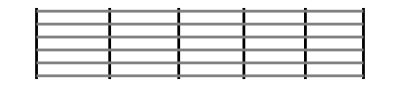

```mathematica
FretBoard[5]
```

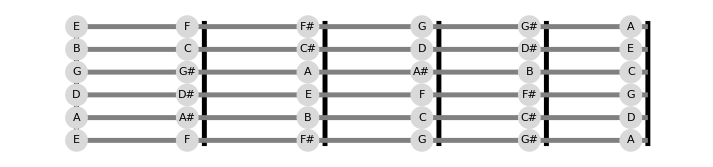

```mathematica
FretBoard[5, Markers->LabelAllNotes]
```

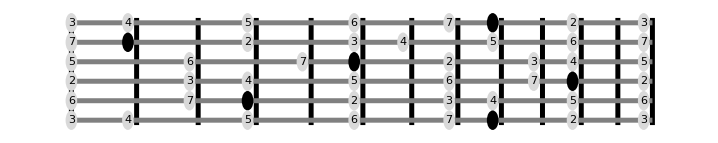

```mathematica
FretBoard[12,Markers->CMajorScale]
```

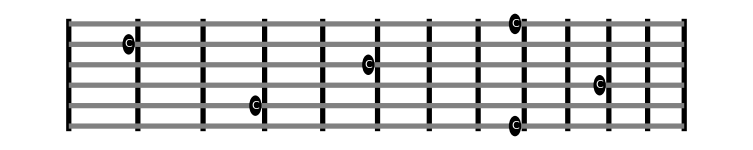

```mathematica
FretBoard[12,Markers->LabelOneNote["C"]]
```

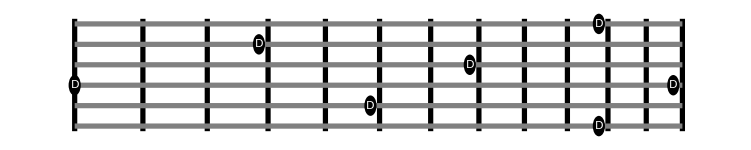

```mathematica
FretBoard[12,Markers->LabelOneNote["D"]]
```

```mathematica
MajorScale[tonic_]:=
Module[{scale=noteNames/@Mod[{2,4,5,7,9,11}+noteNumbers[[tonic]],12,1]},
Function[{note,position},
If[
note==tonic,
BlackDot[position[[1]],position[[2]],note],
If[
MemberQ[scale,note],
LightGrayDot[position[[1]],position[[2]],note],
Nothing
]
]
]
]
```

```mathematica
MajorScale["C"]
```

Function[{note$,position$},If[note$==C,BlackDot[position$⟦1⟧,position$⟦2⟧,note$],If[MemberQ[scale$21543,note$],LightGrayDot[position$⟦1⟧,position$⟦2⟧,note$],Nothing]]]

```mathematica
f=MajorScale["C"]
```

Function[{note$,position$},If[note$==C,BlackDot[position$⟦1⟧,position$⟦2⟧,note$],If[MemberQ[scale$21707,note$],LightGrayDot[position$⟦1⟧,position$⟦2⟧,note$],Nothing]]]

```mathematica
f["C",{1,1}]
```

{GrayLevel[0],Disk[{1-1/2^(1/12)-1.5 dotSize,5 stringSpacing},dotSize],GrayLevel[1],Text[C,{1-1/2^(1/12)-1.5 dotSize,5 stringSpacing},{0,0}]}

```mathematica
f["D",{1,1}]
```

{GrayLevel[0.85],Disk[{1-1/2^(1/12)-1.5 dotSize,5 stringSpacing},dotSize],GrayLevel[0],Text[D,{1-1/2^(1/12)-1.5 dotSize,5 stringSpacing},{0,0}]}

```mathematica
f["C#",{1,2}]
```

Nothing

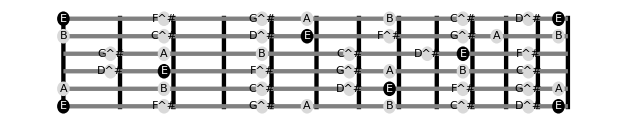

```mathematica
FretBoard[12,Markers->MajorScale["E"],dotScale->12]
```

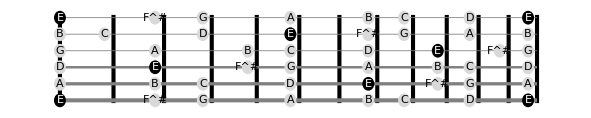

```mathematica
FretBoard[12,Markers->MinorScale["E"]]
```

```mathematica
L1={"a","b","c","d","e","f"};
L2={1,2,3,4,5,6};
```

```mathematica
L1
```

{a,b,c,d,e,f}

```mathematica
Riffle[L1,L2]
```

{a,1,b,2,c,3,d,4,e,5,f,6}

```mathematica
Thin
```

```mathematica
t={Thickness[0.001],Thickness[0.001],Thickness[0.001],Thickness[0.003],Thickness[0.004],Thickness[0.005]};
```

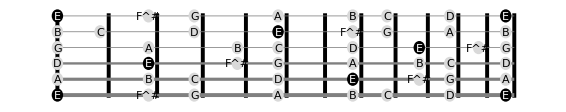

```mathematica
FretBoard[12,Markers->MinorScale["E"],stringThicknesses->t]
```

```mathematica
RelativeInterval[note_,tonic_]:=
Mod[noteNumbers[[note]]-noteNumbers[[tonic]],12]
```

```mathematica
RelativeIntervalLabel[note_,tonic_]:=
scaleLabels[RelativeInterval[note,tonic]]
```

```mathematica
RelativeInterval["C","C"]
```

0

```mathematica
RelativeInterval["B","C"]
```

11

```mathematica
RelativeInterval["D","A"]
```

5

```mathematica
RelativeIntervalLabel["E","C"]
```

3

```mathematica
RelativeInterval["E","C"]
```

4

```mathematica
scaleLabels
```

<|0→R,1→♭2,2→2,3→♭3,4→3,5→4,6→♭5,7→5,8→♭6,9→6,10→♭7,11→7|>

```mathematica
scaleLabels[4]
```

3

```mathematica
RelativeIntervalLabel["G^#","C"]
```

♭6

```mathematica
Keys[noteNumbers]
```

{E,F,F^#,G,G^#,A,A^#,B,C,C^#,D,D^#}

```mathematica
CreatePalette[PasteButton[#]&/@Keys[noteNumbers]]
```

7bx9q_shm33FrontEndObject[LinkObject["7bx9q_shm", 3, 1]]33Untitled-4

```mathematica
PasteButton[#]&/@Keys[noteNumbers]
```

{E,F,F^#,G,G^#,A,A^#,B,C,C^#,D,D^#}

```mathematica
Button["F sharp",Paste["F^#"]]
```

F sharp

```mathematica
F^#
```

```mathematica
CreatePalette[Grid[Partition[Button[#,Paste[#]]&/@Keys[noteNumbers],3],Spacings->{0,0}]]
```

v8jks_shm31FrontEndObject[LinkObject["v8jks_shm", 3, 1]]31Untitled-4

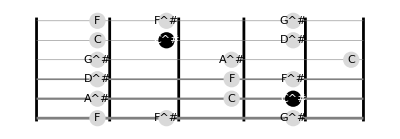

```mathematica
FretBoard[5,Markers->MajorScale["C^#"]]
```

```mathematica
Style["F#",8]
```

F#

```mathematica
CreatePalette[Grid[Partition[PasteButton[Style[#,12],RawBoxes[#],ImageSize->24]&/@Keys[noteNumbers],3],Spacings->{0,0}]]
```

v8jks_shm45FrontEndObject[LinkObject["v8jks_shm", 3, 1]]45Untitled-11

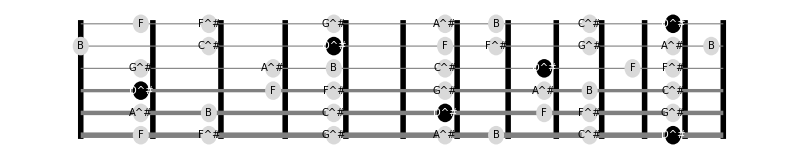

```mathematica
FretBoard[12,Markers->MinorScale["D^#"],dotTextSize->10]
```

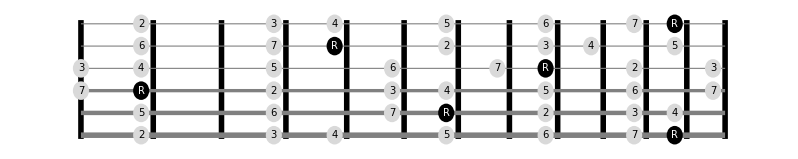

```mathematica
FretBoard[12,Markers->ScaleMarkers["D^#",majorScale,labels->RelativeIntervalLabel],dotTextSize->10]
```

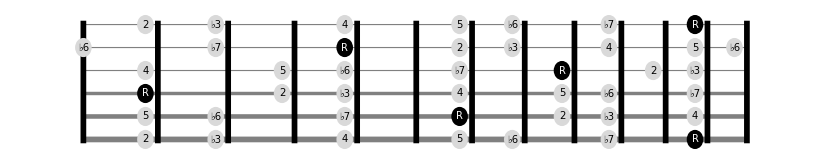

```mathematica
FretBoard[12,Markers->ScaleMarkers["D^#",naturalMinorScale,labels->RelativeIntervalLabel],dotTextSize->10]
```

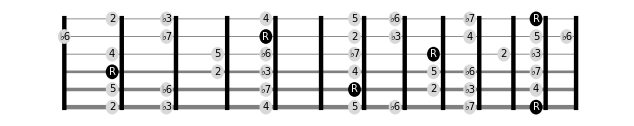

```mathematica
FretBoard[{0,12},Markers->ScaleMarkers["D^#",naturalMinorScale,labels->RelativeIntervalLabel],dotTextSize->10]
```

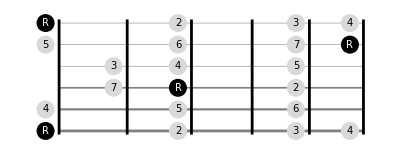

```mathematica
FretBoard[{3,8},Markers->ScaleMarkers["G",majorScale,labels->RelativeIntervalLabel],dotTextSize->10]
```

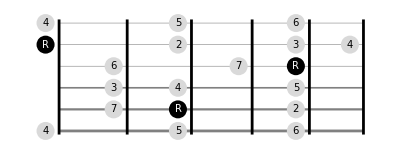

```mathematica
FretBoard[{3,8},DotPosition[s_, f_]:={FretPosition[f]-dotSize*1.5,StringPos[s]};
```

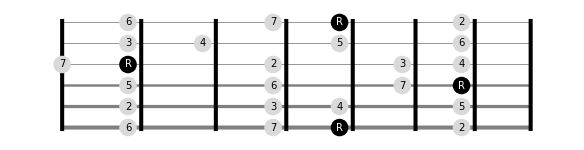

```mathematica
FretBoard[{0,7},Markers->ScaleMarkers["G^#",majorScale,labels->RelativeIntervalLabel],dotTextSize->10]
```

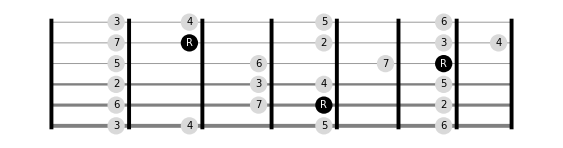

```mathematica
FretBoard[{0,7},Markers->ScaleMarkers["C^#",majorScale,labels->RelativeIntervalLabel],dotTextSize->10]
```

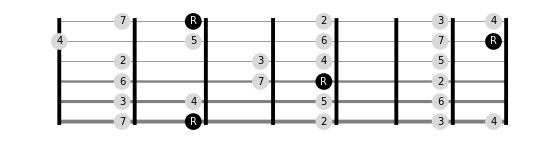

```mathematica
FretBoard[{0,7},Markers->ScaleMarkers["F^#",majorScale,labels->RelativeIntervalLabel],dotTextSize->10]
```

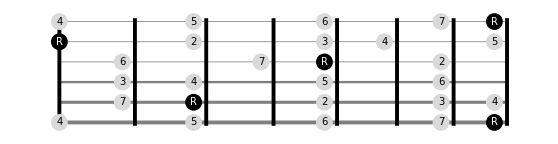

```mathematica
FretBoard[{0,7},Markers->ScaleMarkers["B",majorScale,labels->RelativeIntervalLabel],dotTextSize->10]
```

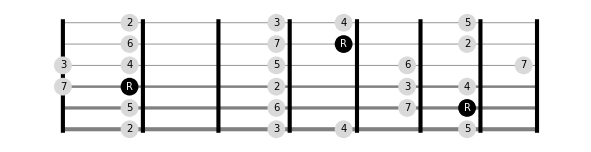

```mathematica
FretBoard[{0,7},Markers->ScaleMarkers["D^#",majorScale,labels->RelativeIntervalLabel],dotTextSize->10]
```

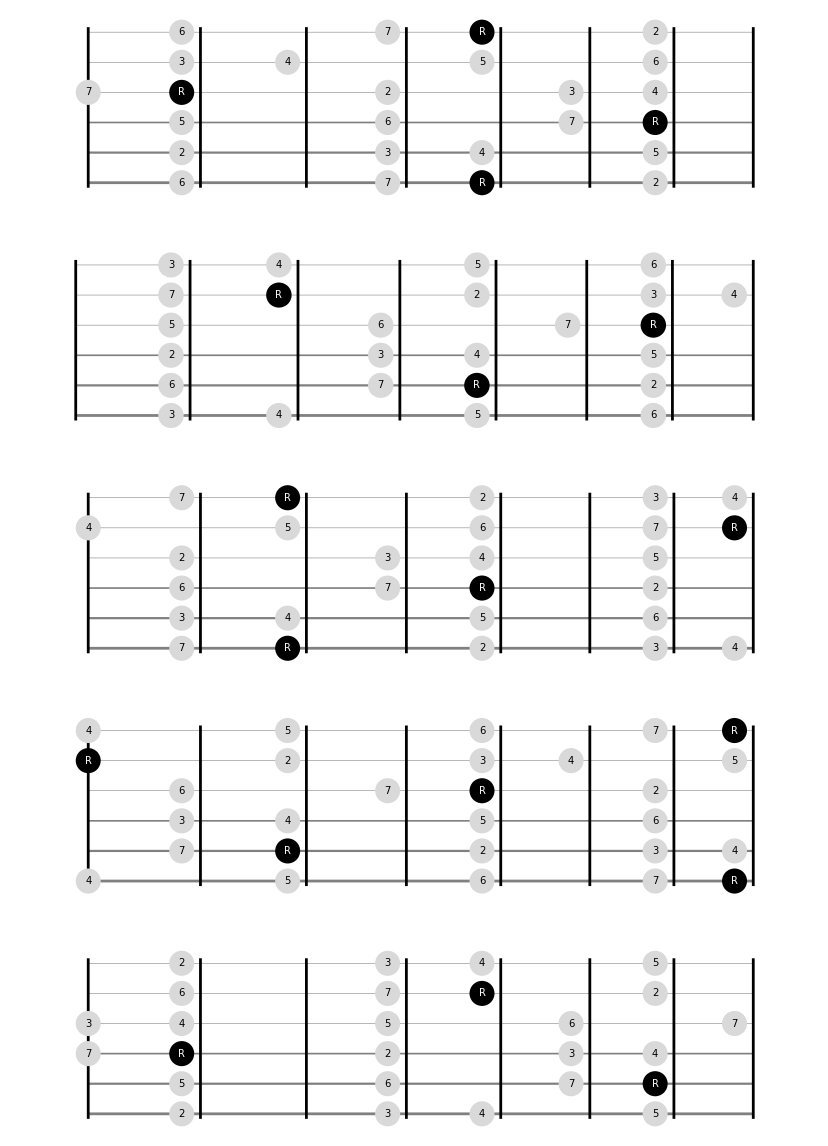

```mathematica
GraphicsColumn[
FretBoard[{0,7},Markers->ScaleMarkers[#,majorScale,labels->RelativeIntervalLabel],dotTextSize->10] & /@{"G^#","C^#","F^#","B","D^#"}]
```

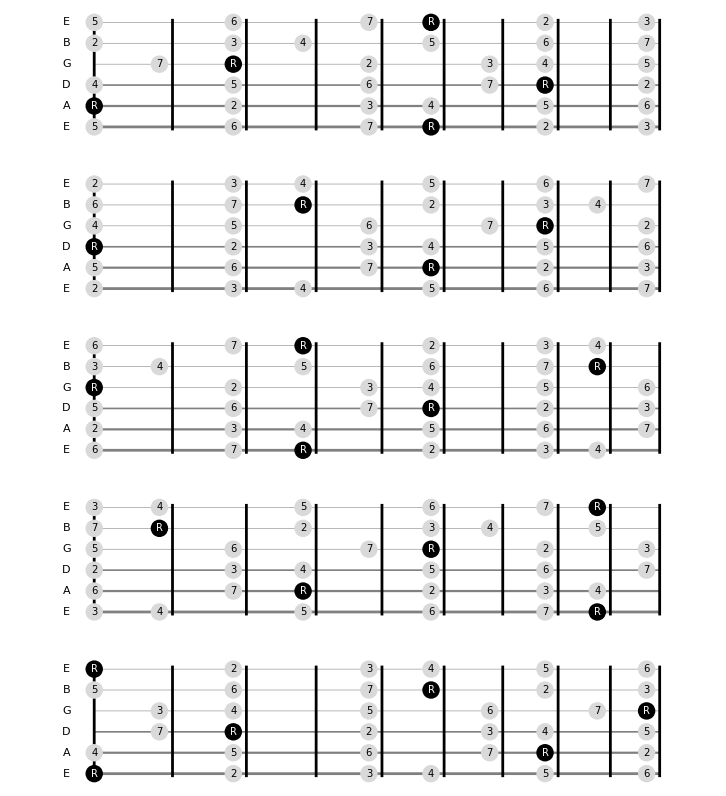

```mathematica
GraphicsColumn[
FretBoard[{0,9},Markers->ScaleMarkers[#,majorScale,labels->RelativeIntervalLabel],dotTextSize->10] & /@{"A","D","G","C","E"},
PlotLabel->"Major Scales"
]
```

```mathematica
Export["/Users/johann/Dropbox/projects/fretboard/Major Scales.pdf",%51,"PDF"]
```

/Users/johann/Dropbox/projects/fretboard/Major Scales.pdf

```mathematica
Export["/Users/johann/Dropbox/projects/fretboard/scales.pdf",%102,"PDF"]
```

/Users/johann/Dropbox/projects/fretboard/scales.pdf

```mathematica
?ScaleMarkers
```

Global`ScaleMarkers

ScaleMarkers[tonic_,intervals_,OptionsPattern[]]:=Module[{scale=noteNames/@Mod[Rest[intervals]+noteNumbers⟦tonic⟧,12,1],labelFunc=OptionValue[labels]},Function[{note,position},If[note==tonic,BlackDot[position⟦1⟧,position⟦2⟧,labelFunc[note,tonic]],If[MemberQ[scale,note],LightGrayDot[position⟦1⟧,position⟦2⟧,labelFunc[note,tonic]],Nothing]]]]
 
Options[ScaleMarkers]={labels→Function[{note,tonic},note]}

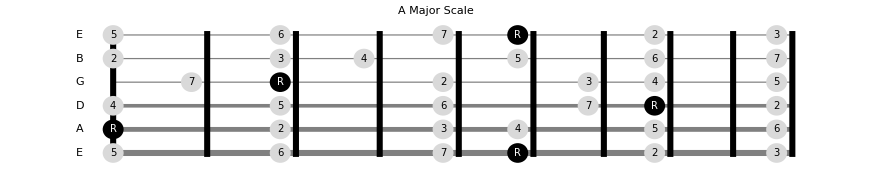

```mathematica
FretBoard[{0,9},Markers->ScaleMarkers["A",majorScale,labels->RelativeIntervalLabel],dotTextSize->10,PlotLabel->"A Major Scale"]
```

```mathematica
labels={"E","B","G","D","A","E"};
ycoords={1,2,3,4,5,6};
xcoords=ConstantArray[0,6];
coords=Transpose[{xcoords,ycoords}];
Thread[Text[labels, coords,{1,0}],List,2]
```

{Text[E,{0,1},{1,0}],Text[B,{0,2},{1,0}],Text[G,{0,3},{1,0}],Text[D,{0,4},{1,0}],Text[A,{0,5},{1,0}],Text[E,{0,6},{1,0}]}

```mathematica
StringPos /@ {1,2,3,4,5,6}
```

{5 stringSpacing,4 stringSpacing,3 stringSpacing,2 stringSpacing,stringSpacing,0}

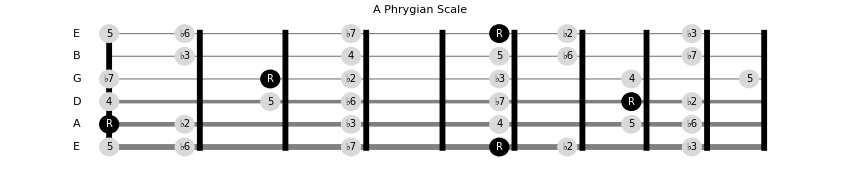

```mathematica
FretBoard[{0,9},Markers->ScaleMarkers["A",phrygianScale,labels->RelativeIntervalLabel],dotTextSize->10,PlotLabel->"A Phrygian Scale"]
```

```mathematica
RomanNumeral[12]
```

XII